```mathematica
Column[IntegerPartitions[5]]
```

{5}
{4,1}
{3,2}
{3,1,1}
{2,2,1}
{2,1,1,1}
{1,1,1,1,1}

```mathematica
NumberPartitions[n_Integer] := Length[IntegerPartitions[n]]
```

```mathematica
NumberPartitions[10]
```

42

```mathematica
Table[Length[IntegerPartitions[10,{n}]],{n,10}]
```

{1,5,8,9,7,5,3,2,1,1}

```mathematica
AddSubNumberPartitions[n_Integer] := ReplacePart[Table[Total[Length[IntegerPartitions[n-m,{#}]]&/@Range[m]],{m,n}],{n -> 1}]
```

```mathematica
AddSubNumberPartitions[10]
```

{1,5,8,9,7,5,3,2,1,1}

```mathematica
Total[AddSubNumberPartitions[10]]
```

42

```mathematica
Needs["Combinatorica`"]
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

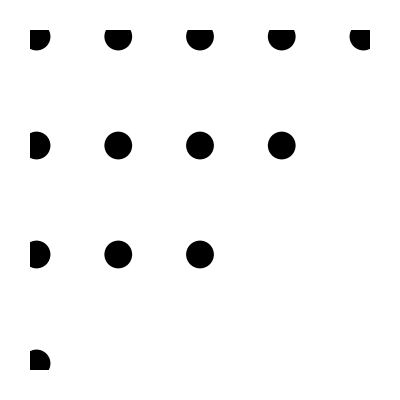

```mathematica
FerrersDiagram[{5,4,3,1}]
```

```mathematica
list[t_Integer,m_Integer]:=Table[Count[#,n],{n,t}] &/@ Select[IntegerPartitions[t],MemberQ[#,m]&]
```

```mathematica
list[8,3]
```

{{0,0,1,0,1,0,0,0},{1,0,1,1,0,0,0,0},{0,1,2,0,0,0,0,0},{2,0,2,0,0,0,0,0},{1,2,1,0,0,0,0,0},{3,1,1,0,0,0,0,0},{5,0,1,0,0,0,0,0}}

```mathematica
CompareList[t_Integer,m_Integer] := Join[{Total[Take[#,m-1]],Part[#,m]-1,Total[#]-Total[Take[#,m-1]]-Part[#,m]}] &/@ list[t,m]
```

```mathematica
CompareList[8,3]
```

{{0,0,1},{1,0,1},{1,1,0},{2,1,0},{3,0,0},{4,0,0},{5,0,0}}

```mathematica
FindLower[t_Integer,m_Integer]/;t>m := Mean[Part[#,1]/Total[#]&/@CompareList[t,m]]
```

```mathematica
FindEqual[t_Integer,m_Integer] /;t>m:= Mean[Part[#,2]/Total[#]&/@CompareList[t,m]]
```

```mathematica
FindHigher[t_Integer,m_Integer] /;t>m:= Mean[Part[#,3]/Total[#]&/@CompareList[t,m]]
```

```mathematica
FindLower[8,3]
```

2/3

```mathematica
FindEqual[8,3]
```

5/42

```mathematica
FindHigher[8,3]
```

3/14

```mathematica
Manipulate[PieChart[{Labeled[FindLower[n,m],N[FindLower[n,m],4]],Labeled[FindEqual[n,m],N[FindEqual[n,m],4]],Labeled[FindHigher[n,m],N[FindHigher[n,m],4]]},ChartLegends -> {"Lower","Equal","Higher"}],{n,2,50,1},{m,1,n-1,1}]
```

```mathematica
GraphLoEqHi[t_Integer] := ListLinePlot[{FindLower[t,#]&/@Range[t-1],FindEqual[t,#]&/@Range[t-1],FindHigher[t,#]&/@Range[t-1]}, PlotLegends->{"Lower","Equal","Higher"}]
```

```mathematica
Manipulate[GraphLoEqHi[n],{n,2,20,1}]
```